```mathematica
ClearAll["Global`*"]
```

```mathematica
f[θ_,b_,c_,d_]=d*Tan[ArcSin[(b*Sin[θ])/(√(b^2+c^2-2*b*c*Cos[θ]))]]
g[θ_,b_,d_,e_]=b*Cos[θ]+√((-2*b*Cos[θ])^2-4(b^2-((b*Sin[θ])/Sin[ArcTan[e/d]])^2))
x=π/3;
y=36;
z=2;
fe[c_]=f[x,y,c,z]
gc[e_]=g[x,y,z,e]
```

(b d Sin[θ])/(√(b^2+c^2-2 b c Cos[θ]) √(1-(b^2 Sin[θ]^2)/(b^2+c^2-2 b c Cos[θ])))

b Cos[θ]+√(4 b^2 Cos[θ]^2-4 (b^2-(b^2 d^2 (1+e^2/d^2) Sin[θ]^2)/e^2))

(10 √3)/(√(100-10 c+c^2) √(1-75/(100-10 c+c^2)))

5+√(100-4 (100-(300 (1+e^2/4))/e^2))

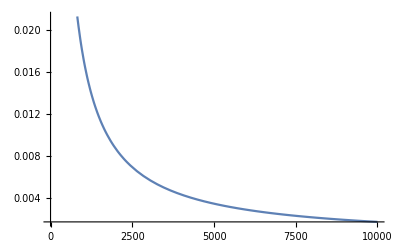

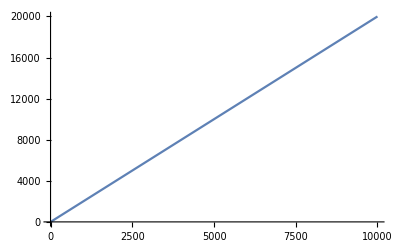

```mathematica
Plot[fe[c],{c,0,10000}]
Plot[gc[fe[c]],{c,0,10000}]
```